```mathematica
circle3D[centre_:{0,0,0},radius_:1,normal_:{0,0,1},angle_:{0,2 Pi}]:=Composition[Line,Map[RotationTransform[{{0,0,1},normal},centre],#]&,Map[Append[#,Last@centre]&,#]&,Append[DeleteDuplicates[Most@#],Last@#]&,Level[#,{-2}]&,MeshPrimitives[#,1]&,DiscretizeRegion,If][First@Differences@angle>=2 Pi,Circle[Most@centre,radius],Circle[Most@centre,radius,angle]]
```

```mathematica
ClearAll[MPLColorMap]
<<"http://pastebin.com/raw/pFsb4ZBS";
cm=72/2.54;
```

```mathematica
cmData=Import[NotebookDirectory[]<>"twilight.csv"];
cmap[x_]:=Blend[Thread[RGBColor[cmData]],x];
```

```mathematica
tmp=BarLegend[{Function[x,cmap[3/(2π)x]],{0,(2π)/3}},LegendLayout->"Row"]
```

```mathematica
Export[NotebookDirectory[]<>"colorbar.png",tmp,ImageResolution->600]
```

/Users/kjmbishop/Bishop Group Dropbox/Bishop Group/Figures/Ongoing Projects/rheotaxis/Figures/DesignedField/colorbar.png

## Design Space m=3

We will consider only the k=0,1 modes, which include n=0,±1,±2,±3,±4.  This function is parameterized by constants c_0,c_1,d_1,c_2,d_2,c_3,d_3,c_4,d_4

```mathematica
FullSimplify[
(c0{0,0,1} +(* n = 0 *)
(c1{1,-I,0}+d1{I,1,0})Exp[I t] +(* n = 1 *)
(-I d1{1,I,0}+ I c1{-I,1,0})Exp[-I t]+(* n = -1 *)
(c2{1,I,0}+d2 {-I,1,0} )Exp[2 I t]+ (* n = 2 *)
(c2{1,-I,0}+d2 {I,1,0} )Exp[-2 I t]+ (* n = -2 *)
(c3{0,0,1}+d3 {0,0,I} )Exp[3 I t]+ (* n = 3 *)
(c3{0,0,1}-d3 {0,0,I} )Exp[-3 I t] +(* n = -3 *)
(c4{1,-I,0}+d4 {I,1,0} )Exp[4 I t]+ (* n = 4 *)
(c4{1,I,0}+d4 {-I,1,0} )Exp[-4 I t](* n = -4 *)
)
]//MatrixForm
```

(2 (c1 Cos[t]+c2 Cos[2 t]+c4 Cos[4 t]-d1 Sin[t]+d2 Sin[2 t]-d4 Sin[4 t])
2 (d1 Cos[t]+d2 Cos[2 t]+d4 Cos[4 t]+c1 Sin[t]-c2 Sin[2 t]+c4 Sin[4 t])
c0+2 c3 Cos[3 t]-2 d3 Sin[3 t])

```mathematica
Manipulate[
ParametricPlot3D[
{ c1 Cos[t]+c2 Cos[2 t]+c4 Cos[4 t]-d1 Sin[t]+d2 Sin[2 t]-d4 Sin[4 t], d1 Cos[t]+d2 Cos[2 t]+d4 Cos[4 t]+c1 Sin[t]-c2 Sin[2 t]+c4 Sin[4 t],1/2 c0+ c3 Cos[3 t]- d3 Sin[3 t]},{t,0,2π},
ColorFunction->Function[{x,y,z,t},Hue[t]],
PlotRange->5{{-1,1},{-1,1},{-1,1}}],
{{c0,0},-1,1},{{c1,0},-1,1},{{d1,0},-1,1},{{c2,0},-1,1},{{d2,0},-1,1},{{c3,0},-1,1},{{d3,0},-1,1},{{c4,0},-1,1},{{d4,0},-1,1}]
```

There are 9 parameters a_0,a_1,b_1,a_2,b_2,a_3,b_3,a_4,b_4, each of which can take a value on the domain -1<a<1.

### Symmetries

```mathematica
B={ c1 Cos[t]+c2 Cos[2 t]+c4 Cos[4 t]-d1 Sin[t]+d2 Sin[2 t]-d4 Sin[4 t], d1 Cos[t]+d2 Cos[2 t]+d4 Cos[4 t]+c1 Sin[t]-c2 Sin[2 t]+c4 Sin[4 t],1/2 c0+ c3 Cos[3 t]- d3 Sin[3 t]};
```

Note: we use coordinate rotations, Mathematica uses vector rotations.  These differ by the sign of the rotation angle.

```mathematica
ν3=2π/3;
FullSimplify[(RotationMatrix[-ν3,{0,0,1}].B)==(B/.t->t-ν3)]
```

True

## Simulate Dynamics (Euler Angles)

### Run & Visualize

Coefficients.

```mathematica
ωN=0.4;
ΓN=0.02;
coeff={-0.5354857771728522,-0.0640346938119043,0.12295670551175342,-0.2855573492821398,-0.017906572239526825,0.6696893933812651,-1.0,-0.1572387671276676,0.45833069489424255};
```

```mathematica
ωN=0.2;
ΓN=0.02;
coeff={-0.5008915662682218,0.03946152115264524,-0.07872720910889322,0.1044431769062875,0.10203828841892518,1.0,-0.16049841425927908,0.059666092094783074,-0.14681309211242283};
```

Parameters

```mathematica
αN=0.577;
βN=0.213;
κN=0.108;
μN=0.873;
λN=1.87;
accuracy=10;
precision=10;
tMax=100 Max[2π/Abs[ωN],1];
```

```mathematica
param=Join[
Thread[{a0,a1,b1,a2,b2,a3,b3,a4,b4}->coeff],
{ω->ωN,Γ->ΓN,α->αN,β->βN,κ->κN,μ->μN,λ->λN,ν->νN,σ->σN}];
```

Initial Conditions
	ϕ(0)=ϕ_IC (not relevant to dynamics)
	θ(0)=θ_IC
	ψ(0)=ψ_IC

```mathematica
rhsIC=Simplify[{
-Cot[θ[t]](B1 Cos[ψ[t]]+B2 Sin[ψ[t]])-(β+κ α)Γ Csc[θ[t]]Sin[ψ[t]],
-Cos[θ[t]](B2 Cos[ψ[t]]-B1 Sin[ψ[t]])-B3 Sin[θ[t]] -(β+κ α) Γ Cos[ψ[t]],
1/2((1+λ)+(1-λ)Cos[2θ[t]])Csc[θ[t]](B1 Cos[ψ[t]]+B2 Sin[ψ[t]])+(β+κ α)Γ Cot[θ[t]]Sin[ψ[t]],
κ (B1 Cos[θ[t]]-B3 Sin[ψ[t]]Sin[θ[t]]),
κ(B2 Cos[θ[t]]+B3 Cos[ψ[t]]Sin[θ[t]])+(μ α +κ β)Γ}/.Thread[{B1,B2,B3}->{0,0,1}]/.param];
```

```mathematica
(* integrate from 0 to tMax *)
solIC=NDSolve[Join[
Thread[{ϕ'[t],θ'[t],ψ'[t],x'[t],y'[t]}==rhsIC],
{ϕ[0]==0,θ[0]==0.1,ψ[0]==0,x[0]==0,y[0]==0}],
{ϕ[t],θ[t],ψ[t],x[t],y[t]},
{t,0,tMax},
PrecisionGoal->precision,AccuracyGoal->accuracy];
```

```mathematica
ϕIC=ϕ[t]/.solIC[[1]]/.t->tMax;
θIC=θ[t]/.solIC[[1]]/.t->tMax;
ψIC=ψ[t]/.solIC[[1]]/.t->tMax;
```

Phase & orientation of the field
The applied phase can be transformed as 

	B(ω t)=R_z(ν)B_ref(ω t+σ)

where ν is the rotation angle and σ is the relative phase.  Note that ν=-σ=(2π)/3 leaves the field unchanged.

```mathematica
νN=0;
σN=0;
```

```mathematica
B={a1 Cos[T]+a2 Cos[2 T]+a4 Cos[4 T]-b1 Sin[T]+b2 Sin[2 T]-b4 Sin[4 T],b1 Cos[T]+b2 Cos[2 T]+b4 Cos[4 T]+a1 Sin[T]-a2 Sin[2 T]+a4 Sin[4 T],a0/2+a3 Cos[3 T]+b3 Sin[3 T]};
```

```mathematica
Manipulate[
Show[ParametricPlot3D[
RotationMatrix[-ν,{0,0,1}].B/.{T->t+σ}/.Thread[{a0,a1,b1,a2,b2,a3,b3,a4,b4}->coeff],{t,0,2π},
ColorFunction->Function[{x,y,z,t},Hue[Mod[t,2π]]],
PlotRange->3{{-1,1},{-1,1},{-1,1}}],
Graphics3D[{Black,Sphere[RotationMatrix[-ν,{0,0,1}].B/.{T->σ}/.Thread[{a0,a1,b1,a2,b2,a3,b3,a4,b4}->coeff],0.1]}]
],
{{ν,0},-π,π},{{σ,0},-π,π}]
```

Equations of motion

```mathematica
rhs=Simplify[{
-Cot[θ[t]](B1 Cos[ψ[t]]+B2 Sin[ψ[t]])-(β+κ α)Γ Csc[θ[t]]Sin[ψ[t]],
-Cos[θ[t]](B2 Cos[ψ[t]]-B1 Sin[ψ[t]])-B3 Sin[θ[t]] -(β+κ α) Γ Cos[ψ[t]],
1/2((1+λ)+(1-λ)Cos[2θ[t]])Csc[θ[t]](B1 Cos[ψ[t]]+B2 Sin[ψ[t]])+(β+κ α)Γ Cot[θ[t]]Sin[ψ[t]],
κ (B1 Cos[θ[t]]-B3 Sin[ψ[t]]Sin[θ[t]]),
κ(B2 Cos[θ[t]]+B3 Cos[ψ[t]]Sin[θ[t]])+(μ α +κ β)Γ}/.Thread[{B1,B2,B3}->(RotationMatrix[-ν,{0,0,1}].B/.{T->ω t+σ})]/.param];
```

```mathematica
(* integrate from 0 to tMax *)
sol=NDSolve[Join[
Thread[{ϕ'[t],θ'[t],ψ'[t],x'[t],y'[t]}==rhs],
{ϕ[0]==ϕIC,θ[0]==θIC,ψ[0]==ψIC,x[0]==0,y[0]==0}],
{ϕ[t],θ[t],ψ[t],x[t],y[t]},
{t,0,tMax},
PrecisionGoal->precision,AccuracyGoal->accuracy];
```

```mathematica
(* integrate from tMax to 2 tMax *)
solCycle=NDSolve[{
Thread[{ϕ'[t],θ'[t],ψ'[t],x'[t],y'[t]}==rhs],
ϕ[tMax]==(ϕ[t]/.sol[[1]]/.t->tMax),
θ[tMax]==(θ[t]/.sol[[1]]/.t->tMax),
ψ[tMax]==(ψ[t]/.sol[[1]]/.t->tMax),
x[tMax]==0,
y[tMax]==0},
{ϕ[t],θ[t],ψ[t],x[t],y[t]},
{t,tMax,2tMax},
PrecisionGoal->precision,AccuracyGoal->accuracy];
```

```mathematica
UxAvg=1/tMax((x[t]/. solCycle[[1]]/.t->2tMax)-(x[t]/. solCycle[[1]]/.t->tMax))
UyAvg=1/tMax((y[t]/. solCycle[[1]]/.t->2tMax)-(y[t]/. solCycle[[1]]/.t->tMax))
```

0.00176999

-0.00890646

Magnetic moment

```mathematica
mCalc[t_]={Sin[θ[t]] Sin[ψ[t]],-Cos[ψ[t]] Sin[θ[t]],Cos[θ[t]]}/.solCycle[[1]];
```

```mathematica
Show[ParametricPlot3D[mCalc[t],{t,2tMax-5 2π/ωN,2tMax},
ColorFunctionScaling->False,
AxesLabel->{"x","y","z"},
PlotRange->{{-1,1},{-1,1},{-1,1}},
LabelStyle->Directive[Black,FontSize->12],
ColorFunction->Function[{x,y,z,t},Hue[Mod[ωN t,2π]/(2π)]]],
Graphics3D[{GrayLevel[0.9],Opacity[0.5],Sphere[]},
Lighting->"Neutral"]]
```

-Graphics3D-

Field

```mathematica
FindMaximum[Norm[B/.param],T]
```

{1.2668,{T→0.999774}}

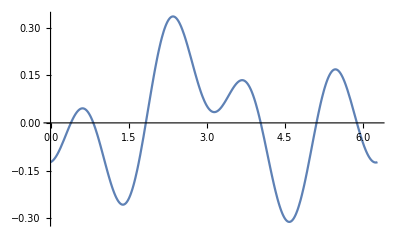

```mathematica
Plot[B[[2]]/.param,{T,0,2π}]
```

```mathematica
solT=FindRoot[Norm[B[[2]]/.param],{T,0.8}]
```

{T→0.822525}

```mathematica
T0=T/.solT[[1]];
νPlot=0;
RνPlot=RotationMatrix[-νPlot,{0,0,1}];
range=1.3;
origin=range{-0.5+0.05,-0.5+0.05,-1+0.05};
vlength=0.5;
side1=Show[
ParametricPlot3D[RνPlot.B/.param,{T,0,2π},ColorFunction->Function[{x,y,z,u},cmap[Mod[3/(2π)Mod[u,(2π)/3],1]]],
ColorFunctionScaling->False,
PlotRange->{0.5{-1,1},0.5{-1,1},{-1,1}}range,
Axes->False,
ImageSize->10 cm,
ViewVertical->{0,0,1},
ImageSize->5 cm,
ViewPoint->2{2,-5,3},
PlotStyle->AbsoluteThickness[2],
Boxed->True,
BoxStyle->Directive[Black,AbsoluteThickness[0.5]],
ImagePadding->{{0.5 cm,0.5cm},{0.5 cm,0.5 cm}}],

ParametricPlot3D[r RνPlot.B/.param,{T,0,2π},{r,0,1},
ColorFunction->Function[{x,y,z,u},cmap[3/(2π)Mod[u,(2π)/3]]],
ColorFunctionScaling->False,
PlotStyle->Opacity[0.1],
Mesh->None,
PlotPoints->100,
PlotRange->{{-1,1},{-1,1},{-1,1}}range],

Graphics3D[{GrayLevel[0.9],(*Polygon[scale{{-1,-1,-1},{-1,1,-1},{1,1,-1},{1,-1,-1}}],*)
cmap[3/(2π)Mod[T0,(2π)/3]],
Arrowheads[0.05],Arrow[Tube[{{0,0,0},RνPlot.B/.param/.T->T0},0.015]],
Black,
Arrowheads[0.04],
Arrow[Tube[{origin,origin+vlength{1,0,0}},0.01]],
Arrow[Tube[{origin,origin+vlength{0,1,0}},0.01]],
Arrow[Tube[{origin,origin+vlength{0,0,1}},0.01]]}]]
```

-Graphics3D-

```mathematica
top1=Show[
ParametricPlot3D[RνPlot.B/.param,{T,0,2π},ColorFunction->Function[{x,y,z,u},cmap[Mod[3/(2π)Mod[u,(2π)/3],1]]],
ColorFunctionScaling->False,
PlotRange->{{-0.5,0.5},{-0.5,0.5},{-1,1}}range,
Axes->False,
ImageSize->10 cm,
ViewVertical->{0,0,1},
ImageSize->5 cm,
ViewPoint->2{0,0,10},
PlotStyle->AbsoluteThickness[2],
Boxed->True,
BoxStyle->Directive[Black,AbsoluteThickness[0.5]],
ImagePadding->{{0.5 cm,0.5cm},{0.5 cm,0.5 cm}}],

ParametricPlot3D[r RνPlot.B/.param,{T,0,2π},{r,0,1},
ColorFunction->Function[{x,y,z,u},cmap[3/(2π)Mod[u,(2π)/3]]],
ColorFunctionScaling->False,
PlotStyle->Opacity[0.1],
Mesh->None,
PlotPoints->100],

Graphics3D[{GrayLevel[0.9],(*Polygon[scale{{-1,-1,-1},{-1,1,-1},{1,1,-1},{1,-1,-1}}],*)
cmap[3/(2π)Mod[T0,(2π)/3]],
Arrowheads[0.05],Arrow[Tube[{{0,0,0},RνPlot.B/.param/.T->T0},0.015]],
Black,
Arrowheads[0.04],
Arrow[Tube[{origin,origin+vlength{1,0,0}},0.01]],
Arrow[Tube[{origin,origin+vlength{0,1,0}},0.01]],
Arrow[Tube[{origin,origin+vlength{0,0,1}},0.01]]}]]
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"OptUpStream_Field1.png",side1, ImageResolution->600]
Export[NotebookDirectory[]<>"OptUpStream_Field2.png",top1, ImageResolution->600]
```

/Users/kjmbishop/Bishop Group Dropbox/Bishop Group/Figures/Ongoing Projects/rheotaxis/Figures/DesignedField/OptUpStream_Field1.png

/Users/kjmbishop/Bishop Group Dropbox/Bishop Group/Figures/Ongoing Projects/rheotaxis/Figures/DesignedField/OptUpStream_Field2.png

Trajectory

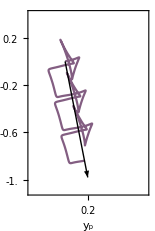

```mathematica
xmin=-0.3;
Δx=1;
ymin=-1.1;
Δy=1.5;
width=3;
trajectory=ParametricPlot[{x[t]/.solCycle[[1]],y[t]/.solCycle[[1]]},{t,tMax,tMax+3 2π/ωN},
ColorFunction->Function[{x,y,t},cmap[Mod[3/(2π)Mod[ωN t,(2π)/3],1]]],
ColorFunctionScaling->False,

Frame->True,
PlotRange->{{xmin,xmin+Δx},{ymin,ymin+Δy}},
PlotStyle->Directive[Black],
AxesStyle->Directive[Black,AbsoluteThickness[0.5]],
LabelStyle->Directive[Black,FontSize->7,ScriptMinSize->2],
FrameStyle->Directive[Black,AbsoluteThickness[0.5]],
FrameTicksStyle->Directive[Black,AbsoluteThickness[0.5]],
AspectRatio->Δy/Δx,
ImagePadding->{{2cm,0.5cm},{2 cm,0.5cm}},
ImageSize->{(width+2.5)cm,(width Δy/Δx+2.5)cm},
FrameTicks->{{Table[i,{i,-1,0.4,0.2}],None},{Table[i,{i,-0.4,0.6,0.2}],None}},
FrameLabel->{Style["x_p",FontSize->9],Style["y_p",FontSize->9]},
Epilog->{Black,AbsoluteThickness[1],Arrowheads[0.1],Arrow[{{0,0},{UxAvg/(√(UxAvg^2+UyAvg^2)),UyAvg/(√(UxAvg^2+UyAvg^2))}}]}]
```

```mathematica
Export[NotebookDirectory[]<>"trajectory.pdf",trajectory]
```

/Users/kjmbishop/Bishop Group Dropbox/Bishop Group/Figures/Ongoing Projects/rheotaxis/Figures/DesignedField/trajectory.pdf

### Make a function that computes velocity

```mathematica
Clear[CalcVelocity]
CalcVelocity[ω_?NumericQ,Γ_?NumericQ,ν_?NumericQ,σ_?NumericQ,ic_,coeff_]:=Module[{α,β,κ,μ,λ,rhs,solCycle,tMax,UxAvg,UyAvg,B1,B2,B3,ϕ,θ,ψ,x,y,t,a0,a1,b1,a2,b2,a3,b3,a4,b4,field,ϕIC,θIC,ψIC,T,sol,accuracy,precision,rhsIC, solIC},
α=0.577;
β=0.213;
κ=0.108;
μ=0.873;
λ=1.87;
accuracy=10;
precision=10;
tMax=100 Max[2π/Abs[ω],1];

{a0,a1,b1,a2,b2,a3,b3,a4,b4}=coeff;

field={
a1 Cos[T]+a2 Cos[2 T]+a4 Cos[4 T]-b1 Sin[T]+b2 Sin[2T]-b4 Sin[4 T],
b1 Cos[T]+b2 Cos[2 T]+b4 Cos[4 T]+a1 Sin[T]-a2 Sin[2T]+a4 Sin[4 T],
1/2 a0+a3 Cos[3 T]+b3 Sin[3 T]};

If[Length[ic] ==3,
{ϕIC,θIC,ψIC}=ic,

(* integrate for initial condition *)
rhsIC=Simplify[{
-Cot[θ[t]](B1 Cos[ψ[t]]+B2 Sin[ψ[t]])-(β+κ α)Γ Csc[θ[t]]Sin[ψ[t]],
-Cos[θ[t]](B2 Cos[ψ[t]]-B1 Sin[ψ[t]])-B3 Sin[θ[t]] -(β+κ α) Γ Cos[ψ[t]],
1/2((1+λ)+(1-λ)Cos[2θ[t]])Csc[θ[t]](B1 Cos[ψ[t]]+B2 Sin[ψ[t]])+(β+κ α)Γ Cot[θ[t]]Sin[ψ[t]],
κ (B1 Cos[θ[t]]-B3 Sin[ψ[t]]Sin[θ[t]]),
κ(B2 Cos[θ[t]]+B3 Cos[ψ[t]]Sin[θ[t]])+(μ α +κ β)Γ}/.Thread[{B1,B2,B3}->{0,0,1}]/.param];

(* integrate from 0 to tMax *)
solIC=NDSolve[Join[
Thread[{ϕ'[t],θ'[t],ψ'[t],x'[t],y'[t]}==rhsIC],
{ϕ[0]==0,θ[0]==0.1,ψ[0]==0,x[0]==0,y[0]==0}],
{ϕ[t],θ[t],ψ[t],x[t],y[t]},
{t,0,tMax},
PrecisionGoal->precision,AccuracyGoal->accuracy];

ϕIC=ϕ[t]/.solIC[[1]]/.t->tMax;
θIC=θ[t]/.solIC[[1]]/.t->tMax;
ψIC=ψ[t]/.solIC[[1]]/.t->tMax
];

rhs={
-Cot[θ[t]](B1 Cos[ψ[t]]+B2 Sin[ψ[t]])-(β+κ α)Γ Csc[θ[t]]Sin[ψ[t]],
-Cos[θ[t]](B2 Cos[ψ[t]]-B1 Sin[ψ[t]])-B3 Sin[θ[t]] -(β+κ α) Γ Cos[ψ[t]],
1/2((1+λ)+(1-λ)Cos[2θ[t]])Csc[θ[t]](B1 Cos[ψ[t]]+B2 Sin[ψ[t]])+(β+κ α)Γ Cot[θ[t]]Sin[ψ[t]],
κ (B1 Cos[θ[t]]-B3 Sin[ψ[t]]Sin[θ[t]]),
κ(B2 Cos[θ[t]]+B3 Cos[ψ[t]]Sin[θ[t]])+(μ α +κ β)Γ}/.Thread[{B1,B2,B3}->(RotationMatrix[-ν,{0,0,1}].field/.T->ω t+σ)];

(* integrate from 0 to tMax *)
sol=NDSolve[{
Thread[{ϕ'[t],θ'[t],ψ'[t],x'[t],y'[t]}==rhs],
ϕ[0]==ϕIC,θ[0]==θIC,ψ[0]==ψIC,x[0]==0,y[0]==0},
{ϕ[t],θ[t],ψ[t],x[t],y[t]},
{t,0,tMax},
PrecisionGoal->precision,AccuracyGoal->accuracy];

(* integrate from tMax to 2 tMax *)
solCycle=NDSolve[{
Thread[{ϕ'[t],θ'[t],ψ'[t],x'[t],y'[t]}==rhs],
ϕ[tMax]==(ϕ[t]/.sol[[1]]/.t->tMax),
θ[tMax]==(θ[t]/.sol[[1]]/.t->tMax),
ψ[tMax]==(ψ[t]/.sol[[1]]/.t->tMax),
x[tMax]==0,
y[tMax]==0},
{ϕ[t],θ[t],ψ[t],x[t],y[t]},
{t,tMax,2tMax},
PrecisionGoal->precision,AccuracyGoal->accuracy];

UxAvg=1/tMax((x[t]/. solCycle[[1]]/.t->2tMax)-(x[t]/. solCycle[[1]]/.t->tMax));
UyAvg=1/tMax((y[t]/. solCycle[[1]]/.t->2tMax)-(y[t]/. solCycle[[1]]/.t->tMax));

{UxAvg,UyAvg}
]
```

```mathematica
CalcVelocity[ωN,ΓN,νN,σN,{ϕIC,θIC,ψIC},coeff]
```

{-0.00864903,0.00916041}

```mathematica
CalcVelocity[ωN,ΓN,νN,σN,False,coeff]
```

{-0.00864903,0.00916041}

### Sensitivities

#### Rotation ν

```mathematica
points=120;
dataν=ParallelTable[Flatten[{ν, CalcVelocity[ωN,ΓN,ν,σN,{ϕIC,θIC,ψIC},coeff]}],{ν,0,2π,(2π)/points}];
```

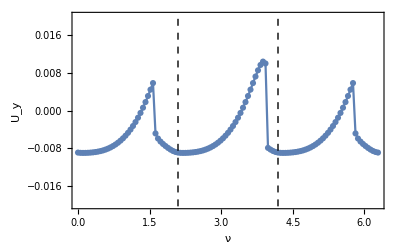

```mathematica
ListPlot[dataν[[All,{1,3}]],
LabelStyle->Directive[Black,FontSize->12],
Frame->True,
PlotRange->{{0,2π},{-0.02,0.02}},
FrameLabel->{"ν","U_y"},
Joined->True,
PlotMarkers->Automatic,
Epilog->{Dashed,Line[{{2π/3,-1},{2π/3,1}}],Line[{{4π/3,-1},{4π/3,1}}]}]
```

#### Phase σ

```mathematica
dataσ=ParallelTable[Flatten[{σ, CalcVelocity[ωN,ΓN,νN,σ,{ϕIC,θIC,ψIC},coeff]}],{σ,0,2π,(2π)/points}];
```

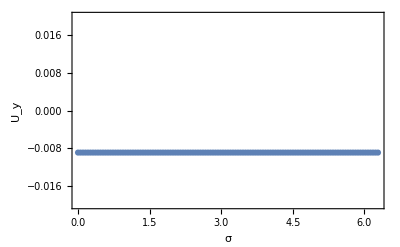

```mathematica
ListPlot[dataσ[[All,{1,3}]],
LabelStyle->Directive[Black,FontSize->12],
Frame->True,
PlotRange->{{0,2π},{-0.02,0.02}},
FrameLabel->{"σ","U_y"},
Joined->True,
PlotMarkers->Automatic]
```

#### Initial θ_IC

```mathematica
dataθIC=ParallelTable[Flatten[{θ, CalcVelocity[ωN,ΓN,νN,σN,{ϕIC,θ,ψIC},coeff]}],{θ,0+π/points,π-π/points,π/(points+2)}];
```

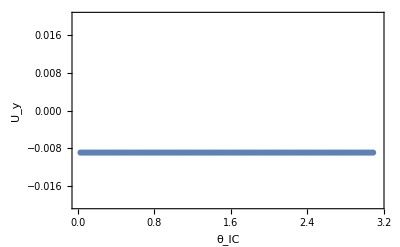

```mathematica
ListPlot[dataθIC[[All,{1,3}]],
LabelStyle->Directive[Black,FontSize->12],
Frame->True,
PlotRange->{{0,π},{-0.02,0.02}},
FrameLabel->{"θ_IC","U_y"},
Joined->True,
PlotMarkers->Automatic]
```

#### Initial ψ_IC

```mathematica
dataψIC=ParallelTable[Flatten[{ψ, CalcVelocity[ωN,ΓN,νN,σN,{ϕIC,θIC,ψ},coeff]}],{ψ,0+π/points,π-π/points,π/(points+2)}];
```

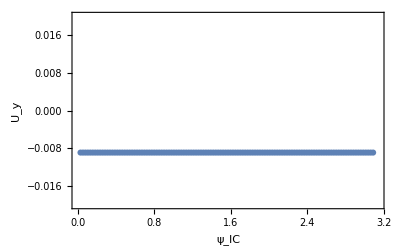

```mathematica
ListPlot[dataψIC[[All,{1,3}]],
LabelStyle->Directive[Black,FontSize->12],
Frame->True,
PlotRange->{{0,π},{-0.02,0.02}},
FrameLabel->{"ψ_IC","U_y"},
Joined->True,
PlotMarkers->Automatic]
```

## Simulate Dynamics (Quaternions)

### Run & Visualize

Equations of motion

```mathematica
rhs={1/2 (β Γ q1[t]+α Γ κ q1[t]-B1 q0[t]^2 q2[t]+B1 q1[t]^2 q2[t]+B1 q2[t]^3+2 B3 q0[t] (q1[t]^2+q2[t]^2)-B1 q2[t] q3[t]^2-2 B2 λ q3[t] (q0[t] q2[t]+q1[t] q3[t])+2 B1 λ q3[t] (-q0[t] q1[t]+q2[t] q3[t])+B2 q1[t] (q0[t]^2-q1[t]^2-q2[t]^2+q3[t]^2)),1/2 (-β Γ q0[t]-α Γ κ q0[t]+B1 q0[t]^2 q3[t]-B1 q1[t]^2 q3[t]-B1 q2[t]^2 q3[t]+B1 q3[t]^3-2 B2 λ q2[t] (q0[t] q2[t]+q1[t] q3[t])+2 B1 λ q2[t] (-q0[t] q1[t]+q2[t] q3[t])+B2 q0[t] (-q0[t]^2+q1[t]^2+q2[t]^2-q3[t]^2)-2 B3 q1[t] (q0[t]^2+q3[t]^2)),1/2 (Γ (β+α κ) q3[t]+2 B2 λ q1[t] (q0[t] q2[t]+q1[t] q3[t])+2 B1 λ q1[t] (q0[t] q1[t]-q2[t] q3[t])-2 B3 q2[t] (q0[t]^2+q3[t]^2)+B1 q0[t] (q0[t]^2-q1[t]^2-q2[t]^2+q3[t]^2)+B2 q3[t] (q0[t]^2-q1[t]^2-q2[t]^2+q3[t]^2)),1/2 (-β Γ q2[t]-α Γ κ q2[t]+2 B3 q1[t]^2 q3[t]+2 B3 q2[t]^2 q3[t]+2 B2 λ q0[t] (q0[t] q2[t]+q1[t] q3[t])+B2 q2[t] (-q0[t]^2+q1[t]^2+q2[t]^2-q3[t]^2)+B1 ((-1+2 λ) q0[t]^2 q1[t]-2 λ q0[t] q2[t] q3[t]+q1[t] (q1[t]^2+q2[t]^2-q3[t]^2))),κ (-2 B3 (q0[t] q2[t]+q1[t] q3[t])+B1 (q0[t]^2-q1[t]^2-q2[t]^2+q3[t]^2)),β Γ κ+α Γ μ+2 B3 κ q0[t] q1[t]-2 B3 κ q2[t] q3[t]+B2 κ (q0[t]^2-q1[t]^2-q2[t]^2+q3[t]^2)}/.Thread[{B1,B2,B3}->(RotationMatrix[-ν,{0,0,1}].B/.{T->ω t+σ})]/.param;
```

Initial condition

-Graphics-

```mathematica
qIC={
Cos[ϕIC/2]Cos[θIC/2]Cos[ψIC/2]-Sin[ϕIC/2]Cos[θIC/2]Sin[ψIC/2],
Cos[ϕIC/2]Sin[θIC/2]Cos[ψIC/2]+Sin[ϕIC/2]Sin[θIC/2]Sin[ψIC/2],
Cos[ϕIC/2]Sin[θIC/2]Sin[ψIC/2]-Sin[ϕIC/2]Sin[θIC/2]Cos[ψIC/2],
Cos[ϕIC/2]Cos[θIC/2]Sin[ψIC/2]+Sin[ϕIC/2]Cos[θIC/2]Cos[ψIC/2]
}
```

{0.999996,-0.00275317,0.,0.}

```mathematica
(* integrate from 0 to tMax *)
sol=NDSolve[Join[
Thread[{q0'[t],q1'[t],q2'[t],q3'[t],x'[t],y'[t]}==rhs],
Thread[{q0[0],q1[0],q2[0],q3[0]}==qIC],{x[0]==0,y[0]==0}],
{q0[t],q1[t],q2[t],q3[t],x[t],y[t]},
{t,0,tMax},
PrecisionGoal->precision,AccuracyGoal->accuracy];
```

```mathematica
(* integrate from tMax to 2 tMax *)
solCycle=NDSolve[{
Thread[{q0'[t],q1'[t],q2'[t],q3'[t],x'[t],y'[t]}==rhs],
q0[tMax]==(q0[t]/.sol[[1]]/.t->tMax),
q1[tMax]==(q1[t]/.sol[[1]]/.t->tMax),
q2[tMax]==(q2[t]/.sol[[1]]/.t->tMax),
q3[tMax]==(q3[t]/.sol[[1]]/.t->tMax),
x[tMax]==0,
y[tMax]==0},
{q0[t],q1[t],q2[t],q3[t],x[t],y[t]},
{t,tMax,2tMax},
PrecisionGoal->precision,AccuracyGoal->accuracy];
```

```mathematica
UxAvg=1/tMax((x[t]/. solCycle[[1]]/.t->2tMax)-(x[t]/. solCycle[[1]]/.t->tMax))
UyAvg=1/tMax((y[t]/. solCycle[[1]]/.t->2tMax)-(y[t]/. solCycle[[1]]/.t->tMax))
```

0.00177075

-0.00890647

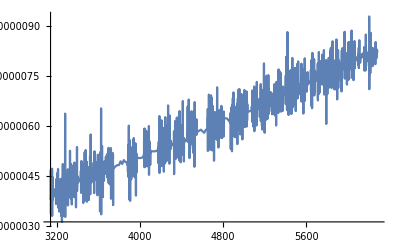

```mathematica
Plot[q3[t]^2+q2[t]^2+q1[t]^2+q0[t]^2/.solCycle[[1]],{t,tMax,2tMax}]
```

Magnetic moment

```mathematica
mCalcq[t_]={2 q0[t] q2[t]+2 q1[t] q3[t],-2 q0[t] q1[t]+2 q2[t] q3[t],q0[t]^2-q1[t]^2-q2[t]^2+q3[t]^2}/.solCycle[[1]];
```

```mathematica
Show[ParametricPlot3D[{mCalcq[t]},{t,2tMax-5 2π/ωN,2tMax},
ColorFunctionScaling->False,
AxesLabel->{"x","y","z"},
PlotRange->{{-1,1},{-1,1},{-1,1}},
LabelStyle->Directive[Black,FontSize->12],
ColorFunction->Function[{x,y,z,t},Hue[Mod[ωN t,2π]/(2π)]]],
Graphics3D[{GrayLevel[0.9],Opacity[0.5],Sphere[]},
Lighting->"Neutral"]]
```

-Graphics3D-

### Make a function that computes velocity

```mathematica
Clear[CalcVelocityq]
CalcVelocityq[ω_?NumericQ,Γ_?NumericQ,ν_?NumericQ,σ_?NumericQ,ic_,coeff_]:=Module[{α,β,κ,μ,λ,rhs,solCycle,tMax,UxAvg,UyAvg,B1,B2,B3,q0,q1,q2,q3,x,y,t,a0,a1,b1,a2,b2,a3,b3,a4,b4,field,ϕIC,θIC,ψIC,qIC,T,sol,accuracy,precision},
α=0.577;
β=0.213;
κ=0.108;
μ=0.873;
λ=1.87;
accuracy=10;
precision=10;
tMax=100 Max[2π/Abs[ω],1];

{a0,a1,b1,a2,b2,a3,b3,a4,b4}=coeff;
{ϕIC,θIC,ψIC}=ic;

qIC={
Cos[ϕIC/2]Cos[θIC/2]Cos[ψIC/2]-Sin[ϕIC/2]Cos[θIC/2]Sin[ψIC/2],
Cos[ϕIC/2]Sin[θIC/2]Cos[ψIC/2]+Sin[ϕIC/2]Sin[θIC/2]Sin[ψIC/2],
Cos[ϕIC/2]Sin[θIC/2]Sin[ψIC/2]-Sin[ϕIC/2]Sin[θIC/2]Cos[ψIC/2],
Cos[ϕIC/2]Cos[θIC/2]Sin[ψIC/2]+Sin[ϕIC/2]Cos[θIC/2]Cos[ψIC/2]
};

field={
a1 Cos[T]+a2 Cos[2 T]+a4 Cos[4 T]-b1 Sin[T]+b2 Sin[2T]-b4 Sin[4 T],
b1 Cos[T]+b2 Cos[2 T]+b4 Cos[4 T]+a1 Sin[T]-a2 Sin[2T]+a4 Sin[4 T],
1/2 a0+a3 Cos[3 T]+b3 Sin[3 T]};

rhs={1/2 (β Γ q1[t]+α Γ κ q1[t]-B1 q0[t]^2 q2[t]+B1 q1[t]^2 q2[t]+B1 q2[t]^3+2 B3 q0[t] (q1[t]^2+q2[t]^2)-B1 q2[t] q3[t]^2-2 B2 λ q3[t] (q0[t] q2[t]+q1[t] q3[t])+2 B1 λ q3[t] (-q0[t] q1[t]+q2[t] q3[t])+B2 q1[t] (q0[t]^2-q1[t]^2-q2[t]^2+q3[t]^2)),1/2 (-β Γ q0[t]-α Γ κ q0[t]+B1 q0[t]^2 q3[t]-B1 q1[t]^2 q3[t]-B1 q2[t]^2 q3[t]+B1 q3[t]^3-2 B2 λ q2[t] (q0[t] q2[t]+q1[t] q3[t])+2 B1 λ q2[t] (-q0[t] q1[t]+q2[t] q3[t])+B2 q0[t] (-q0[t]^2+q1[t]^2+q2[t]^2-q3[t]^2)-2 B3 q1[t] (q0[t]^2+q3[t]^2)),1/2 (Γ (β+α κ) q3[t]+2 B2 λ q1[t] (q0[t] q2[t]+q1[t] q3[t])+2 B1 λ q1[t] (q0[t] q1[t]-q2[t] q3[t])-2 B3 q2[t] (q0[t]^2+q3[t]^2)+B1 q0[t] (q0[t]^2-q1[t]^2-q2[t]^2+q3[t]^2)+B2 q3[t] (q0[t]^2-q1[t]^2-q2[t]^2+q3[t]^2)),1/2 (-β Γ q2[t]-α Γ κ q2[t]+2 B3 q1[t]^2 q3[t]+2 B3 q2[t]^2 q3[t]+2 B2 λ q0[t] (q0[t] q2[t]+q1[t] q3[t])+B2 q2[t] (-q0[t]^2+q1[t]^2+q2[t]^2-q3[t]^2)+B1 ((-1+2 λ) q0[t]^2 q1[t]-2 λ q0[t] q2[t] q3[t]+q1[t] (q1[t]^2+q2[t]^2-q3[t]^2))),κ (-2 B3 (q0[t] q2[t]+q1[t] q3[t])+B1 (q0[t]^2-q1[t]^2-q2[t]^2+q3[t]^2)),β Γ κ+α Γ μ+2 B3 κ q0[t] q1[t]-2 B3 κ q2[t] q3[t]+B2 κ (q0[t]^2-q1[t]^2-q2[t]^2+q3[t]^2)}/.Thread[{B1,B2,B3}->(RotationMatrix[-ν,{0,0,1}].field/.{T->ω t+σ})];

(* integrate from 0 to tMax *)
sol=NDSolve[Join[
Thread[{q0'[t],q1'[t],q2'[t],q3'[t],x'[t],y'[t]}==rhs],
Thread[{q0[0],q1[0],q2[0],q3[0]}==qIC],{x[0]==0,y[0]==0}],
{q0[t],q1[t],q2[t],q3[t],x[t],y[t]},
{t,0,tMax},
PrecisionGoal->precision,AccuracyGoal->accuracy];

(* integrate from tMax to 2 tMax *)
solCycle=NDSolve[{
Thread[{q0'[t],q1'[t],q2'[t],q3'[t],x'[t],y'[t]}==rhs],
q0[tMax]==(q0[t]/.sol[[1]]/.t->tMax),
q1[tMax]==(q1[t]/.sol[[1]]/.t->tMax),
q2[tMax]==(q2[t]/.sol[[1]]/.t->tMax),
q3[tMax]==(q3[t]/.sol[[1]]/.t->tMax),
x[tMax]==0,
y[tMax]==0},
{q0[t],q1[t],q2[t],q3[t],x[t],y[t]},
{t,tMax,2tMax},
PrecisionGoal->precision,AccuracyGoal->accuracy];

UxAvg=1/tMax((x[t]/. solCycle[[1]]/.t->2tMax)-(x[t]/. solCycle[[1]]/.t->tMax));
UyAvg=1/tMax((y[t]/. solCycle[[1]]/.t->2tMax)-(y[t]/. solCycle[[1]]/.t->tMax));

{UxAvg,UyAvg}
]
```

```mathematica
CalcVelocityq[ωN,ΓN,νN,σN,{ϕIC,θIC,ψIC},coeff]
```

{0.00177075,-0.00890647}

### Sensitivities

There seem to be  2 attractors: one with a positive (downstream) velocity, another with a negative (upstream) velocity. Each of these attractors is periodic with the driving frequency ω.  For each attractor, the phase of the oscillation does not the time-averaged velocity.

#### Rotation ν

```mathematica
points=240;
dataνq=ParallelTable[Flatten[{ν, CalcVelocityq[ωN,ΓN,ν,0,{0,0,0},coeff]}],{ν,0,2π,(2π)/points}];
```

```mathematica
Mean[dataνq[[All,3]]]
```

-0.00495821

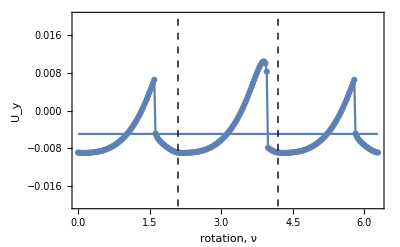

```mathematica
Show[
ListPlot[{dataνq[[All,{1,3}]]},
LabelStyle->Directive[Black,FontSize->12],
Frame->True,
PlotRange->{{0,2π},{-0.02,0.02}},
FrameLabel->{"rotation, ν","U_y"},
Joined->True,
PlotMarkers->Automatic,
Epilog->{Dashed,Line[{{2π/3,-1},{2π/3,1}}],Line[{{4π/3,-1},{4π/3,1}}]}],
Plot[Mean[dataνq[[All,3]]],{x,0,2π}]
]
```

#### Phase σ

```mathematica
dataσq=ParallelTable[Flatten[{σ, CalcVelocityq[ωN,ΓN,0,σ,{0,0,0},coeff]}],{σ,0,2π,(2π)/points}];
```

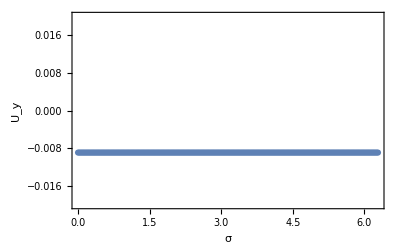

```mathematica
ListPlot[{dataσq[[All,{1,3}]]},
LabelStyle->Directive[Black,FontSize->12],
Frame->True,
PlotRange->{{0,2π},{-0.02,0.02}},
FrameLabel->{"σ","U_y"},
Joined->True,
PlotMarkers->Automatic]
```

#### Initial θ_IC

```mathematica
dataθICq=ParallelTable[Flatten[{θ, CalcVelocityq[ωN,ΓN,0,0,{0,θ,0},coeff]}],{θ,0+π/points,π-π/points,π/(points+2)}];
```

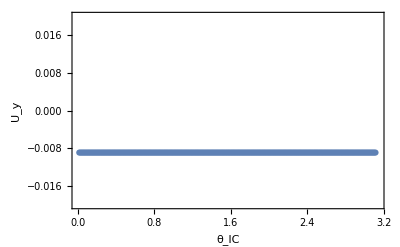

```mathematica
ListPlot[{dataθICq[[All,{1,3}]]},
LabelStyle->Directive[Black,FontSize->12],
Frame->True,
PlotRange->{{0,π},{-0.02,0.02}},
FrameLabel->{"θ_IC","U_y"},
Joined->True,
PlotMarkers->Automatic]
```

### Initial orientation θ(0)=ψ(0)=0

```mathematica
νpoints=30;
σpoints=27;dataνσq=ParallelTable[Flatten[{ν,σ,CalcVelocityq[ωN,ΓN,ν,σ,{0,0,0},coeff]}],{ν,0,2π,(2π)/νpoints},{σ,0,2π,(2π)/σpoints}];
```

```mathematica
Mean[Mean[dataνσq[[All,All,4]]]]
```

-0.00542773

```mathematica
plotData=Transpose[{Flatten[dataνσq[[All,All,1]]],Flatten[dataνσq[[All,All,2]]],Flatten[dataνσq[[All,All,4]]]}];
```

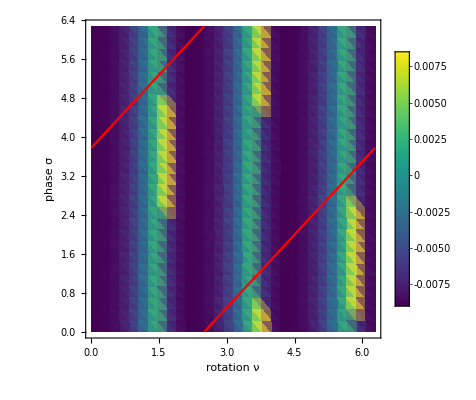

```mathematica
Show[ListDensityPlot[plotData,
PlotRange->{{0,2π},{0,2π}},
PlotLegends->Automatic,
(*PlotRangePadding->0,*)
LabelStyle->Directive[Black,FontSize->12],
FrameLabel->{"rotation ν","phase σ"},
ColorFunction->MPLColorMap["Viridis"],
ColorFunctionScaling->True],
Plot[{Mod[x-2.5,2π]},{x,0,2π},
PlotStyle->Red]
]
```

## Two-limit cycles: Orientation Dependence

We would like to compute the time-averaged velocity for each attractor as a function of the orientation angle ν of the field.  We can do this by sweeping across ν and updating the initial conditions as we go.

```mathematica
Clear[Sweepνq]
Sweepνq[ω_?NumericQ,Γ_?NumericQ,νStart_?NumericQ,σ_?NumericQ,ic_,coeff_,νPoints_?NumericQ,Forward_]:=Module[{α,β,κ,μ,λ,ν,νVal,rhs,solCycle,tMax,UxAvg,UyAvg,B1,B2,B3,q0,q1,q2,q3,x,y,t,a0,a1,b1,a2,b2,a3,b3,a4,b4,field,ϕIC,θIC,ψIC,qIC,T,sol,accuracy,precision},
α=0.577;
β=0.213;
κ=0.108;
μ=0.873;
λ=1.87;
accuracy=10;
precision=10;
tMax=100 (2π/Abs[ω]);

{a0,a1,b1,a2,b2,a3,b3,a4,b4}=coeff;
{ϕIC,θIC,ψIC}=ic;

qIC={
Cos[ϕIC/2]Cos[θIC/2]Cos[ψIC/2]-Sin[ϕIC/2]Cos[θIC/2]Sin[ψIC/2],
Cos[ϕIC/2]Sin[θIC/2]Cos[ψIC/2]+Sin[ϕIC/2]Sin[θIC/2]Sin[ψIC/2],
Cos[ϕIC/2]Sin[θIC/2]Sin[ψIC/2]-Sin[ϕIC/2]Sin[θIC/2]Cos[ψIC/2],
Cos[ϕIC/2]Cos[θIC/2]Sin[ψIC/2]+Sin[ϕIC/2]Cos[θIC/2]Cos[ψIC/2]
};

field={
a1 Cos[T]+a2 Cos[2 T]+a4 Cos[4 T]-b1 Sin[T]+b2 Sin[2T]-b4 Sin[4 T],
b1 Cos[T]+b2 Cos[2 T]+b4 Cos[4 T]+a1 Sin[T]-a2 Sin[2T]+a4 Sin[4 T],
1/2 a0+a3 Cos[3 T]+b3 Sin[3 T]};

rhs={1/2 (β Γ q1[t]+α Γ κ q1[t]-B1 q0[t]^2 q2[t]+B1 q1[t]^2 q2[t]+B1 q2[t]^3+2 B3 q0[t] (q1[t]^2+q2[t]^2)-B1 q2[t] q3[t]^2-2 B2 λ q3[t] (q0[t] q2[t]+q1[t] q3[t])+2 B1 λ q3[t] (-q0[t] q1[t]+q2[t] q3[t])+B2 q1[t] (q0[t]^2-q1[t]^2-q2[t]^2+q3[t]^2)),1/2 (-β Γ q0[t]-α Γ κ q0[t]+B1 q0[t]^2 q3[t]-B1 q1[t]^2 q3[t]-B1 q2[t]^2 q3[t]+B1 q3[t]^3-2 B2 λ q2[t] (q0[t] q2[t]+q1[t] q3[t])+2 B1 λ q2[t] (-q0[t] q1[t]+q2[t] q3[t])+B2 q0[t] (-q0[t]^2+q1[t]^2+q2[t]^2-q3[t]^2)-2 B3 q1[t] (q0[t]^2+q3[t]^2)),1/2 (Γ (β+α κ) q3[t]+2 B2 λ q1[t] (q0[t] q2[t]+q1[t] q3[t])+2 B1 λ q1[t] (q0[t] q1[t]-q2[t] q3[t])-2 B3 q2[t] (q0[t]^2+q3[t]^2)+B1 q0[t] (q0[t]^2-q1[t]^2-q2[t]^2+q3[t]^2)+B2 q3[t] (q0[t]^2-q1[t]^2-q2[t]^2+q3[t]^2)),1/2 (-β Γ q2[t]-α Γ κ q2[t]+2 B3 q1[t]^2 q3[t]+2 B3 q2[t]^2 q3[t]+2 B2 λ q0[t] (q0[t] q2[t]+q1[t] q3[t])+B2 q2[t] (-q0[t]^2+q1[t]^2+q2[t]^2-q3[t]^2)+B1 ((-1+2 λ) q0[t]^2 q1[t]-2 λ q0[t] q2[t] q3[t]+q1[t] (q1[t]^2+q2[t]^2-q3[t]^2))),κ (-2 B3 (q0[t] q2[t]+q1[t] q3[t])+B1 (q0[t]^2-q1[t]^2-q2[t]^2+q3[t]^2)),β Γ κ+α Γ μ+2 B3 κ q0[t] q1[t]-2 B3 κ q2[t] q3[t]+B2 κ (q0[t]^2-q1[t]^2-q2[t]^2+q3[t]^2)}/.Thread[{B1,B2,B3}->(RotationMatrix[-ν,{0,0,1}].field/.{T->ω t+σ})];

(* integrate from 0 to tMax *)
solCycle=NDSolve[{
Thread[{q0'[t],q1'[t],q2'[t],q3'[t],x'[t],y'[t]}==rhs/.ν->νStart],
Thread[{q0[0],q1[0],q2[0],q3[0]}==qIC],
x[0]==0,y[0]==0},
{q0[t],q1[t],q2[t],q3[t],x[t],y[t]},
{t,0,tMax},
PrecisionGoal->precision,AccuracyGoal->accuracy];

qIC={
(q0[t]/.solCycle[[1]]/.t->tMax),
(q1[t]/.solCycle[[1]]/.t->tMax),
(q2[t]/.solCycle[[1]]/.t->tMax),
(q3[t]/.solCycle[[1]]/.t->tMax)
};

ParallelTable[
(* integrate from 0 to tMax *)
solCycle=NDSolve[{
Thread[{q0'[t],q1'[t],q2'[t],q3'[t],x'[t],y'[t]}==rhs/.ν->νVal],
Thread[{q0[0],q1[0],q2[0],q3[0]}==qIC],
x[0]==0,
y[0]==0},
{q0[t],q1[t],q2[t],q3[t],x[t],y[t]},
{t,0,tMax},
PrecisionGoal->precision,AccuracyGoal->accuracy];

UxAvg=2/tMax((x[t]/. solCycle[[1]]/.t->tMax)-(x[t]/. solCycle[[1]]/.t->tMax/2));
UyAvg=2/tMax((y[t]/. solCycle[[1]]/.t->tMax)-(y[t]/. solCycle[[1]]/.t->tMax/2));

qIC={
(q0[t]/.solCycle[[1]]/.t->tMax),
(q1[t]/.solCycle[[1]]/.t->tMax),
(q2[t]/.solCycle[[1]]/.t->tMax),
(q3[t]/.solCycle[[1]]/.t->tMax)
};

{νVal,UxAvg,UyAvg},
If[Forward,
{νVal,0,2π,(2π)/νPoints},
{νVal,2π,0,-(2π)/νPoints}]]
]
```

```mathematica
dataνqF1=Sweepνq[ωN,ΓN,0,0,{0,0,0},coeff,960,True];
dataνqR1=Sweepνq[ωN,ΓN,0,0,{0,0,0},coeff,960,False];
```

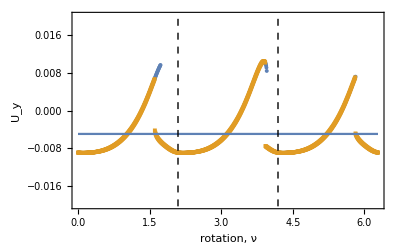

```mathematica
Show[
ListPlot[{dataνqF1[[All,{1,3}]],dataνqR1[[All,{1,3}]]},
LabelStyle->Directive[Black,FontSize->12],
Frame->True,
PlotRange->{{0,2π},{-0.02,0.02}},
FrameLabel->{"rotation, ν","U_y"},
Joined->False,
PlotMarkers->{Automatic,4},
Epilog->{Dashed,Line[{{2π/3,-1},{2π/3,1}}],Line[{{4π/3,-1},{4π/3,1}}]}],
Plot[Mean[dataνq[[All,3]]],{x,0,2π}]
]
```

```mathematica
circle=Graphics[{Black,Disk[{0,0},0.1]}];
```

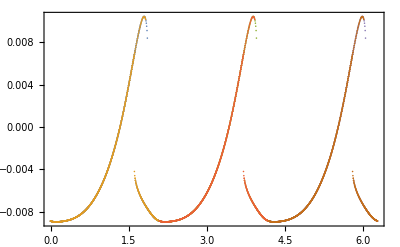

```mathematica
ListPlot[{
Transpose[{Mod[dataνqF1[[All,1]],2π/3],dataνqF1[[All,3]]}],
Transpose[{Mod[dataνqR1[[All,1]],2π/3],dataνqR1[[All,3]]}],
Transpose[{2π/3+Mod[dataνqF1[[All,1]],2π/3],dataνqF1[[All,3]]}],
Transpose[{2π/3+Mod[dataνqR1[[All,1]],2π/3],dataνqR1[[All,3]]}],
Transpose[{4π/3+Mod[dataνqF1[[All,1]],2π/3],dataνqF1[[All,3]]}],
Transpose[{4π/3+Mod[dataνqR1[[All,1]],2π/3],dataνqR1[[All,3]]}]},
Frame->True]
```

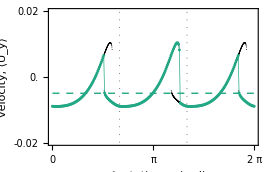

```mathematica
orientationPlot=Show[
ListPlot[{
Transpose[{Mod[dataνqF1[[All,1]],2π/3],dataνqF1[[All,3]]}],
Transpose[{Mod[dataνqR1[[All,1]],2π/3],dataνqR1[[All,3]]}],
Transpose[{2π/3+Mod[dataνqF1[[All,1]],2π/3],dataνqF1[[All,3]]}],
Transpose[{2π/3+Mod[dataνqR1[[All,1]],2π/3],dataνqR1[[All,3]]}],
Transpose[{4π/3+Mod[dataνqF1[[All,1]],2π/3],dataνqF1[[All,3]]}],
Transpose[{4π/3+Mod[dataνqR1[[All,1]],2π/3],dataνqR1[[All,3]]}]},
Frame->True,
PlotRange->{{0,2π},{-0.02,0.02}},
Joined->False,
PlotMarkers->{circle,1},
PlotStyle->Directive[Black],
AxesStyle->Directive[Black,AbsoluteThickness[0.5]],
LabelStyle->Directive[Black,FontSize->7,ScriptMinSize->2],
FrameStyle->Directive[Black,AbsoluteThickness[0.5]],
FrameTicksStyle->Directive[Black,AbsoluteThickness[0.5]],
AspectRatio->4.5/7,
ImageSize->{9.5cm,6.5cm},

FrameTicks->{{Table[i,{i,-0.02,0.02,0.01}],None},{Table[i,{i,0,2π,π/3}],None}},

ImagePadding->{{2cm,0.5cm},{1.5 cm,0.5cm}},
FrameLabel->{Style["orientation, ν (rad)",FontSize->9],Style["velocity, ⟨U_y⟩",FontSize->9]},
Epilog->{Dotted,AbsoluteThickness[0.5],Line[{{2π/3,-1},{2π/3,1}}],Line[{{4π/3,-1},{4π/3,1}}]}],

ListPlot[{dataνq[[All,{1,3}]]},
PlotStyle->Directive[MPLColorMap["Viridis"][0.6],AbsoluteThickness[0.5]],
Joined->True,
PlotMarkers->{Automatic,3}
],

Plot[Mean[dataνq[[All,3]]],{x,0,2π},
PlotStyle->Directive[Dashed,AbsoluteThickness[1],MPLColorMap["Viridis"][0.6]]]
]
```

```mathematica
Export[NotebookDirectory[]<>"orientationPlot.pdf",orientationPlot]
```

/Users/kjmbishop/Bishop Group Dropbox/Bishop Group/Figures/Ongoing Projects/rheotaxis/Figures/DesignedField/orientationPlot.pdf

```mathematica
dataνq[[1,All]]
```

{0,-0.0121161,-0.0119732}

```mathematica
iMin=First@Ordering[dataνq[[All,3]],1]
Mod[dataνq[[iMin,1]]//N,2π/3]
dataνq[[iMin,3]]//N
```

71

1.5708

-0.0151438

## New Field

```mathematica
Clear[T]
field={
a1 Cos[T]+a2 Cos[2 T]+a4 Cos[4 T]-b1 Sin[T]+b2 Sin[2T]-b4 Sin[4 T],
b1 Cos[T]+b2 Cos[2 T]+b4 Cos[4 T]+a1 Sin[T]-a2 Sin[2T]+a4 Sin[4 T],
1/2 a0+a3 Cos[3 T]+b3 Sin[3 T]};
field//MatrixForm
```

(a1 Cos[T]+a2 Cos[2 T]+a4 Cos[4 T]-b1 Sin[T]+b2 Sin[2 T]-b4 Sin[4 T]
b1 Cos[T]+b2 Cos[2 T]+b4 Cos[4 T]+a1 Sin[T]-a2 Sin[2 T]+a4 Sin[4 T]
a0/2+a3 Cos[3 T]+b3 Sin[3 T])

```mathematica
RotationMatrix[-ν,{0,0,1}].field//MatrixForm
```

(Cos[ν] (a1 Cos[T]+a2 Cos[2 T]+a4 Cos[4 T]-b1 Sin[T]+b2 Sin[2 T]-b4 Sin[4 T])+(b1 Cos[T]+b2 Cos[2 T]+b4 Cos[4 T]+a1 Sin[T]-a2 Sin[2 T]+a4 Sin[4 T]) Sin[ν]
Cos[ν] (b1 Cos[T]+b2 Cos[2 T]+b4 Cos[4 T]+a1 Sin[T]-a2 Sin[2 T]+a4 Sin[4 T])-(a1 Cos[T]+a2 Cos[2 T]+a4 Cos[4 T]-b1 Sin[T]+b2 Sin[2 T]-b4 Sin[4 T]) Sin[ν]
a0/2+a3 Cos[3 T]+b3 Sin[3 T])

```mathematica
Collect[(RotationMatrix[-ν,{0,0,1}].field)[[1]],{Cos[2 T]}]
```

a1 Cos[T] Cos[ν]+a4 Cos[4 T] Cos[ν]-b1 Cos[ν] Sin[T]+b2 Cos[ν] Sin[2 T]-b4 Cos[ν] Sin[4 T]+b1 Cos[T] Sin[ν]+b4 Cos[4 T] Sin[ν]+a1 Sin[T] Sin[ν]-a2 Sin[2 T] Sin[ν]+a4 Sin[4 T] Sin[ν]+Cos[2 T] (a2 Cos[ν]+b2 Sin[ν])

```mathematica
Collect[(RotationMatrix[-ν,{0,0,1}].field)[[2]],{Sin[ T]}]
```

b1 Cos[T] Cos[ν]+b2 Cos[2 T] Cos[ν]+b4 Cos[4 T] Cos[ν]-a2 Cos[ν] Sin[2 T]+a4 Cos[ν] Sin[4 T]-a1 Cos[T] Sin[ν]-a2 Cos[2 T] Sin[ν]-a4 Cos[4 T] Sin[ν]-b2 Sin[2 T] Sin[ν]+b4 Sin[4 T] Sin[ν]+Sin[T] (a1 Cos[ν]+b1 Sin[ν])

```mathematica
[
```

a'_0=a_0
a'_3=a_3
b'_3=b_3
a'_1=a_1 cosν+b_1 sinν
a'_2=a_2 cosν+b_2 sinν